```mathematica
JtrigForm[0,0,Pi/2]//MatrixForm//TeXForm
```

\left(
\begin{array}{cccc}
 \frac{1}{\sqrt{2}} & 0 & 0 & -\frac{i}{\sqrt{2}} \\
 0 & \frac{1}{\sqrt{2}} & \frac{i}{\sqrt{2}} & 0 \\
 0 & \frac{i}{\sqrt{2}} & \frac{1}{\sqrt{2}} & 0 \\
 -\frac{i}{\sqrt{2}} & 0 & 0 & \frac{1}{\sqrt{2}} \\
\end{array}
\right)

```mathematica
j = J[0,0,γ];
myFunc[a_]:=ComplexExpand[Conjugate[a]]
```

```mathematica
JtrigForm[a,b,γ]
```

{{ⅇ^(1/2 ⅈ a b γ) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]),ⅇ^(1/2 ⅈ a b γ) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2]),ⅇ^(1/2 ⅈ a b γ) (ⅈ Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]+Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2]),ⅇ^(1/2 ⅈ a b γ) (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])},{-ⅇ^(1/2 ⅈ a b γ) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2]),ⅇ^(1/2 ⅈ a b γ) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]),ⅈ ⅇ^(1/2 ⅈ a b γ) (Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+ⅈ Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]),ⅇ^(1/2 ⅈ a b γ) (ⅈ Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]+Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])},{-ⅈ ⅇ^(1/2 ⅈ a b γ) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2]),ⅈ ⅇ^(1/2 ⅈ a b γ) (Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+ⅈ Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]),ⅇ^(1/2 ⅈ a b γ) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]),ⅇ^(1/2 ⅈ a b γ) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])},{ⅇ^(1/2 ⅈ a b γ) (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]),-ⅈ ⅇ^(1/2 ⅈ a b γ) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2]),-ⅇ^(1/2 ⅈ a b γ) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2]),ⅇ^(1/2 ⅈ a b γ) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])}}

```mathematica
aliceMove
bobsMove
```

{{Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2],Sin[x1] (-ⅈ Cos[y1]-Sin[y1]) Sin[z1/2]},{Sin[x1] (-ⅈ Cos[y1]+Sin[y1]) Sin[z1/2],Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]}}

{{Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2],Sin[x2] (-ⅈ Cos[y1]-Sin[y1]) Sin[z2/2]},{Sin[x2] (-ⅈ Cos[y1]+Sin[y1]) Sin[z2/2],Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]}}

```mathematica
fullPlay =( ( play[J[a,b,γ],aliceMove,bobsMove]//TrigToExp//Simplify)/.Conjugate->myFunc);
```

```mathematica
fullPlay2 = ( ( play[JtrigForm[a,b,γ],aliceMove,bobsMove]));
```

```mathematica
fpSimp = (fullPlay2/.Conjugate->myFunc)//Simplify//FullSimplify;
```

```mathematica
fpSimp
```

{Cos[z1/2] (Cos[z2/2]-ⅈ Cos[γ] Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ]))+1/2 Sin[z1/2] (2 Cos[x1] (Cos[b γ] (-ⅈ Cos[z2/2] Cos[γ]+Sin[z2/2] (-Cos[x2] Cos[a γ]+Cos[y1] Sin[x2] Sin[a γ]))+Sin[x2] Sin[y1] Sin[z2/2] Sin[γ] Sin[b γ])+Sin[x1] (Sin[z2/2] Sin[γ] ((Cos[a γ]+Cos[b γ]) Sin[x2] Sin[2 y1]+2 Cos[x2] Sin[y1] Sin[a γ])+2 Cos[y1] (ⅈ Cos[z2/2] Cos[γ]+Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])) Sin[b γ])),Sin[z2/2] (Cos[z1/2] (Sin[x2] Sin[y1]-ⅈ Cos[x2] Cos[γ] Sin[a γ])+Sin[z1/2] (-Cos[x2] Cos[a γ] Sin[x1] Sin[y1] Sin[γ]+Cos[x1] Cos[b γ] (-ⅈ Cos[γ] Sin[x2] Sin[y1]-Cos[x2] Sin[a γ])))+Cos[y1]^2 Cos[a γ] Sin[x1] Sin[x2] Sin[z1/2] Sin[z2/2] Sin[b γ]-Cos[x1] Cos[z2/2] Sin[z1/2] Sin[γ] Sin[b γ]+Cos[y1] (-ⅈ Cos[z1/2] Cos[γ] Cos[a γ] Sin[x2] Sin[z2/2]+Sin[z1/2] (-Cos[x1] Cos[a γ] Cos[b γ] Sin[x2] Sin[z2/2]+Sin[x1] (-Cos[z2/2] Cos[b γ] Sin[γ]+Sin[z2/2] (Sin[x2] Sin[y1] Sin[γ] Sin[a γ]+(ⅈ Cos[γ] Sin[x2] Sin[y1]+Cos[x2] Sin[a γ]) Sin[b γ])))),Cos[y1]^2 Cos[b γ] Sin[x1] Sin[x2] Sin[z1/2] Sin[z2/2] Sin[a γ]+Cos[z2/2] Sin[z1/2] (Sin[x1] Sin[y1]-ⅈ Cos[x1] Cos[γ] Sin[b γ])+Sin[z2/2] (-Cos[x1] Cos[b γ] Sin[x2] Sin[y1] Sin[z1/2] Sin[γ]+Cos[x2] (-Cos[z1/2] Sin[γ] Sin[a γ]+Cos[a γ] Sin[z1/2] (-ⅈ Cos[γ] Sin[x1] Sin[y1]-Cos[x1] Sin[b γ])))+Cos[y1] (-ⅈ Cos[z2/2] Cos[γ] Cos[b γ] Sin[x1] Sin[z1/2]+Sin[z2/2] (-Cos[x2] Cos[a γ] Cos[b γ] Sin[x1] Sin[z1/2]+Sin[x2] (-Cos[z1/2] Cos[a γ] Sin[γ]+Sin[z1/2] (ⅈ Cos[γ] Sin[x1] Sin[y1] Sin[a γ]+(Sin[x1] Sin[y1] Sin[γ]+Cos[x1] Sin[a γ]) Sin[b γ])))),Cos[z1/2] Sin[z2/2] Sin[γ] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])+1/2 Sin[x1] Sin[z1/2] (Sin[z2/2] (Sin[x2] (1-Cos[y1]^2 (1+2 Cos[a γ] Cos[b γ])+Sin[y1]^2-ⅈ Cos[γ] (Cos[a γ]+Cos[b γ]) Sin[2 y1])-2 Cos[x2] (Cos[y1] Cos[b γ]+ⅈ Cos[γ] Sin[y1]) Sin[a γ])-2 Cos[y1] Cos[z2/2] Sin[γ] Sin[b γ])+Cos[x1] Sin[z1/2] (Cos[z2/2] Cos[b γ] Sin[γ]-Sin[z2/2] (Cos[y1] Cos[a γ] Sin[x2]+ⅈ Cos[γ] Sin[x2] Sin[y1]+Cos[x2] Sin[a γ]) Sin[b γ])}

```mathematica
Clear[n]
```

```mathematica
{{0,1},{1,0}}.su2[Pi/2,Pi/2,2 2 π/n]//FullSimplify//MatrixForm
su2[a,b,-c]//FullSimplify//MatrixForm
```

(Sin[(2 π)/n] | Cos[(2 π)/n]
Cos[(2 π)/n] | -Sin[(2 π)/n])

(Cos[c/2]+ⅈ Cos[a] Sin[c/2] | Sin[a] (ⅈ Cos[b]+Sin[b]) Sin[c/2]
ⅈ ⅇ^(ⅈ b) Sin[a] Sin[c/2] | Cos[c/2]-ⅈ Cos[a] Sin[c/2])

```mathematica
fpSimp[[4]]
```

Cos[z1/2] Sin[z2/2] Sin[γ] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])+1/2 Sin[x1] Sin[z1/2] (Sin[z2/2] (Sin[x2] (1-Cos[y1]^2 (1+2 Cos[a γ] Cos[b γ])+Sin[y1]^2-ⅈ Cos[γ] (Cos[a γ]+Cos[b γ]) Sin[2 y1])-2 Cos[x2] (Cos[y1] Cos[b γ]+ⅈ Cos[γ] Sin[y1]) Sin[a γ])-2 Cos[y1] Cos[z2/2] Sin[γ] Sin[b γ])+Cos[x1] Sin[z1/2] (Cos[z2/2] Cos[b γ] Sin[γ]-Sin[z2/2] (Cos[y1] Cos[a γ] Sin[x2]+ⅈ Cos[γ] Sin[x2] Sin[y1]+Cos[x2] Sin[a γ]) Sin[b γ])

```mathematica
ent = EntanglementMeasureNoReduction[fpSimp]
```

```mathematica
ent//Evaluate
```

```mathematica
varspecs = {
{a,0,10},
{b,0,10},
{γ,0,Pi/2},
{x1,0,Pi},
{y1,0,Pi},
{z1,0,Pi},
{x2,0,Pi},
{y2,0,Pi},
{z2,0,Pi}};
Manipulate[ent//Evaluate,Evaluate[Sequence@@varspecs]]
```

```mathematica
fpSimp[[3]]
```

Cos[y1]^2 Cos[b γ] Sin[x1] Sin[x2] Sin[z1/2] Sin[z2/2] Sin[a γ]+Cos[z2/2] Sin[z1/2] (Sin[x1] Sin[y1]-ⅈ Cos[x1] Cos[γ] Sin[b γ])+Sin[z2/2] (-Cos[x1] Cos[b γ] Sin[x2] Sin[y1] Sin[z1/2] Sin[γ]+Cos[x2] (-Cos[z1/2] Sin[γ] Sin[a γ]+Cos[a γ] Sin[z1/2] (-ⅈ Cos[γ] Sin[x1] Sin[y1]-Cos[x1] Sin[b γ])))+Cos[y1] (-ⅈ Cos[z2/2] Cos[γ] Cos[b γ] Sin[x1] Sin[z1/2]+Sin[z2/2] (-Cos[x2] Cos[a γ] Cos[b γ] Sin[x1] Sin[z1/2]+Sin[x2] (-Cos[z1/2] Cos[a γ] Sin[γ]+Sin[z1/2] (ⅈ Cos[γ] Sin[x1] Sin[y1] Sin[a γ]+(Sin[x1] Sin[y1] Sin[γ]+Cos[x1] Sin[a γ]) Sin[b γ]))))

```mathematica
Entang
```

```mathematica
alicesScore[fpSimp]/.Conjugate->myFunc
```

(Cos[z1/2] Sin[z2/2] Sin[γ] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])-ⅈ (1/2 Sin[x1] Sin[z1/2] Sin[z2/2] (-Cos[γ] (Cos[a γ]+Cos[b γ]) Sin[x2] Sin[2 y1]-2 Cos[x2] Cos[γ] Sin[y1] Sin[a γ])-Cos[x1] Cos[γ] Sin[x2] Sin[y1] Sin[z1/2] Sin[z2/2] Sin[b γ])+1/2 Sin[x1] Sin[z1/2] (Sin[z2/2] (Sin[x2] (1-Cos[y1]^2 (1+2 Cos[a γ] Cos[b γ])+Sin[y1]^2)-2 Cos[x2] Cos[y1] Cos[b γ] Sin[a γ])-2 Cos[y1] Cos[z2/2] Sin[γ] Sin[b γ])+Cos[x1] Sin[z1/2] (Cos[z2/2] Cos[b γ] Sin[γ]-Sin[z2/2] (Cos[y1] Cos[a γ] Sin[x2]+Cos[x2] Sin[a γ]) Sin[b γ])) (Cos[z1/2] Sin[z2/2] Sin[γ] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])+1/2 Sin[x1] Sin[z1/2] (Sin[z2/2] (Sin[x2] (1-Cos[y1]^2 (1+2 Cos[a γ] Cos[b γ])+Sin[y1]^2-ⅈ Cos[γ] (Cos[a γ]+Cos[b γ]) Sin[2 y1])-2 Cos[x2] (Cos[y1] Cos[b γ]+ⅈ Cos[γ] Sin[y1]) Sin[a γ])-2 Cos[y1] Cos[z2/2] Sin[γ] Sin[b γ])+Cos[x1] Sin[z1/2] (Cos[z2/2] Cos[b γ] Sin[γ]-Sin[z2/2] (Cos[y1] Cos[a γ] Sin[x2]+ⅈ Cos[γ] Sin[x2] Sin[y1]+Cos[x2] Sin[a γ]) Sin[b γ]))+3 (Cos[z1/2] Cos[z2/2]-ⅈ (-Cos[z1/2] Cos[γ] Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])+1/2 Sin[z1/2] (-2 Cos[x1] Cos[z2/2] Cos[γ] Cos[b γ]+2 Cos[y1] Cos[z2/2] Cos[γ] Sin[x1] Sin[b γ]))+1/2 Sin[z1/2] (2 Cos[x1] (Cos[b γ] Sin[z2/2] (-Cos[x2] Cos[a γ]+Cos[y1] Sin[x2] Sin[a γ])+Sin[x2] Sin[y1] Sin[z2/2] Sin[γ] Sin[b γ])+Sin[x1] (Sin[z2/2] Sin[γ] ((Cos[a γ]+Cos[b γ]) Sin[x2] Sin[2 y1]+2 Cos[x2] Sin[y1] Sin[a γ])+2 Cos[y1] Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ]) Sin[b γ]))) (Cos[z1/2] (Cos[z2/2]-ⅈ Cos[γ] Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ]))+1/2 Sin[z1/2] (2 Cos[x1] (Cos[b γ] (-ⅈ Cos[z2/2] Cos[γ]+Sin[z2/2] (-Cos[x2] Cos[a γ]+Cos[y1] Sin[x2] Sin[a γ]))+Sin[x2] Sin[y1] Sin[z2/2] Sin[γ] Sin[b γ])+Sin[x1] (Sin[z2/2] Sin[γ] ((Cos[a γ]+Cos[b γ]) Sin[x2] Sin[2 y1]+2 Cos[x2] Sin[y1] Sin[a γ])+2 Cos[y1] (ⅈ Cos[z2/2] Cos[γ]+Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])) Sin[b γ])))+5 (Cos[z2/2] Sin[x1] Sin[y1] Sin[z1/2]+Cos[y1]^2 Cos[b γ] Sin[x1] Sin[x2] Sin[z1/2] Sin[z2/2] Sin[a γ]-ⅈ (-Cos[x2] Cos[γ] Cos[a γ] Sin[x1] Sin[y1] Sin[z1/2] Sin[z2/2]+Cos[y1] (-Cos[z2/2] Cos[γ] Cos[b γ] Sin[x1] Sin[z1/2]+Cos[γ] Sin[x1] Sin[x2] Sin[y1] Sin[z1/2] Sin[z2/2] Sin[a γ])-Cos[x1] Cos[z2/2] Cos[γ] Sin[z1/2] Sin[b γ])+Sin[z2/2] (-Cos[x1] Cos[b γ] Sin[x2] Sin[y1] Sin[z1/2] Sin[γ]+Cos[x2] (-Cos[z1/2] Sin[γ] Sin[a γ]-Cos[x1] Cos[a γ] Sin[z1/2] Sin[b γ]))+Cos[y1] Sin[z2/2] (-Cos[x2] Cos[a γ] Cos[b γ] Sin[x1] Sin[z1/2]+Sin[x2] (-Cos[z1/2] Cos[a γ] Sin[γ]+Sin[z1/2] (Sin[x1] Sin[y1] Sin[γ]+Cos[x1] Sin[a γ]) Sin[b γ]))) (Cos[y1]^2 Cos[b γ] Sin[x1] Sin[x2] Sin[z1/2] Sin[z2/2] Sin[a γ]+Cos[z2/2] Sin[z1/2] (Sin[x1] Sin[y1]-ⅈ Cos[x1] Cos[γ] Sin[b γ])+Sin[z2/2] (-Cos[x1] Cos[b γ] Sin[x2] Sin[y1] Sin[z1/2] Sin[γ]+Cos[x2] (-Cos[z1/2] Sin[γ] Sin[a γ]+Cos[a γ] Sin[z1/2] (-ⅈ Cos[γ] Sin[x1] Sin[y1]-Cos[x1] Sin[b γ])))+Cos[y1] (-ⅈ Cos[z2/2] Cos[γ] Cos[b γ] Sin[x1] Sin[z1/2]+Sin[z2/2] (-Cos[x2] Cos[a γ] Cos[b γ] Sin[x1] Sin[z1/2]+Sin[x2] (-Cos[z1/2] Cos[a γ] Sin[γ]+Sin[z1/2] (ⅈ Cos[γ] Sin[x1] Sin[y1] Sin[a γ]+(Sin[x1] Sin[y1] Sin[γ]+Cos[x1] Sin[a γ]) Sin[b γ])))))

```mathematica
{Cos[z1/2] (Cos[z2/2]-ⅈ Cos[γ] Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ]))+1/2 Sin[z1/2] (2 Cos[x1] (Cos[b γ] (-ⅈ Cos[z2/2] Cos[γ]+Sin[z2/2] (-Cos[x2] Cos[a γ]+Cos[y1] Sin[x2] Sin[a γ]))+Sin[x2] Sin[y1] Sin[z2/2] Sin[γ] Sin[b γ])+Sin[x1] (Sin[z2/2] Sin[γ] ((Cos[a γ]+Cos[b γ]) Sin[x2] Sin[2 y1]+2 Cos[x2] Sin[y1] Sin[a γ])+2 Cos[y1] (ⅈ Cos[z2/2] Cos[γ]+Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])) Sin[b γ])),Sin[z2/2] (Cos[z1/2] (Sin[x2] Sin[y1]-ⅈ Cos[x2] Cos[γ] Sin[a γ])+Sin[z1/2] (-Cos[x2] Cos[a γ] Sin[x1] Sin[y1] Sin[γ]+Cos[x1] Cos[b γ] (-ⅈ Cos[γ] Sin[x2] Sin[y1]-Cos[x2] Sin[a γ])))+Cos[y1]^2 Cos[a γ] Sin[x1] Sin[x2] Sin[z1/2] Sin[z2/2] Sin[b γ]-Cos[x1] Cos[z2/2] Sin[z1/2] Sin[γ] Sin[b γ]+Cos[y1] (-ⅈ Cos[z1/2] Cos[γ] Cos[a γ] Sin[x2] Sin[z2/2]+Sin[z1/2] (-Cos[x1] Cos[a γ] Cos[b γ] Sin[x2] Sin[z2/2]+Sin[x1] (-Cos[z2/2] Cos[b γ] Sin[γ]+Sin[z2/2] (Sin[x2] Sin[y1] Sin[γ] Sin[a γ]+(ⅈ Cos[γ] Sin[x2] Sin[y1]+Cos[x2] Sin[a γ]) Sin[b γ])))),Cos[y1]^2 Cos[b γ] Sin[x1] Sin[x2] Sin[z1/2] Sin[z2/2] Sin[a γ]+Cos[z2/2] Sin[z1/2] (Sin[x1] Sin[y1]-ⅈ Cos[x1] Cos[γ] Sin[b γ])+Sin[z2/2] (-Cos[x1] Cos[b γ] Sin[x2] Sin[y1] Sin[z1/2] Sin[γ]+Cos[x2] (-Cos[z1/2] Sin[γ] Sin[a γ]+Cos[a γ] Sin[z1/2] (-ⅈ Cos[γ] Sin[x1] Sin[y1]-Cos[x1] Sin[b γ])))+Cos[y1] (-ⅈ Cos[z2/2] Cos[γ] Cos[b γ] Sin[x1] Sin[z1/2]+Sin[z2/2] (-Cos[x2] Cos[a γ] Cos[b γ] Sin[x1] Sin[z1/2]+Sin[x2] (-Cos[z1/2] Cos[a γ] Sin[γ]+Sin[z1/2] (ⅈ Cos[γ] Sin[x1] Sin[y1] Sin[a γ]+(Sin[x1] Sin[y1] Sin[γ]+Cos[x1] Sin[a γ]) Sin[b γ])))),Cos[z1/2] Sin[z2/2] Sin[γ] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])+1/2 Sin[x1] Sin[z1/2] (Sin[z2/2] (Sin[x2] (1-Cos[y1]^2 (1+2 Cos[a γ] Cos[b γ])+Sin[y1]^2-ⅈ Cos[γ] (Cos[a γ]+Cos[b γ]) Sin[2 y1])-2 Cos[x2] (Cos[y1] Cos[b γ]+ⅈ Cos[γ] Sin[y1]) Sin[a γ])-2 Cos[y1] Cos[z2/2] Sin[γ] Sin[b γ])+Cos[x1] Sin[z1/2] (Cos[z2/2] Cos[b γ] Sin[γ]-Sin[z2/2] (Cos[y1] Cos[a γ] Sin[x2]+ⅈ Cos[γ] Sin[x2] Sin[y1]+Cos[x2] Sin[a γ]) Sin[b γ])}
```

```mathematica
fullPlay2[[1]]
```

ⅇ^(-1/2 ⅈ a b γ) (-1/256 ⅇ^(-1/2 ⅈ (2 x1+2 x2+z1+z2+2 γ-a b γ)) ((-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1-2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)-2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))+(-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(2 ⅈ x2)) (-1+ⅇ^(ⅈ z1)) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(-ⅈ y1) (-1+ⅇ^(2 ⅈ x2)) (-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(ⅈ z1)) (-1-2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)-2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))) (1+ⅇ^(ⅈ γ) (Cos[a γ]-Cos[b γ]-Cos[(1+a+b) γ]-ⅈ (Sin[a γ]-Sin[b γ]-Sin[(1+a+b) γ])))+1/256 ⅇ^(-1/2 ⅈ (2 x1+2 x2+z1+z2+2 γ-a b γ)) (ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x2)) (-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))+ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(ⅈ z1)) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))+(-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (-ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(2 ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(2 ⅈ x2)) (-1+ⅇ^(ⅈ z1)) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))) (-1+ⅇ^(ⅈ γ) (Cos[a γ]+Cos[b γ]-Cos[(1+a+b) γ]-ⅈ (Sin[a γ]+Sin[b γ]-Sin[(1+a+b) γ])))+1/256 ⅇ^(-1/2 ⅈ (2 x1+2 x2+z1+z2+2 γ-a b γ)) ((-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(2 ⅈ x2)) (-1+ⅇ^(ⅈ z1)) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))+(-1-2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)-2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(-ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(ⅈ z1)) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x2)) (-1-2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)-2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))) (-1+ⅇ^(ⅈ γ) (Cos[a γ]-Cos[b γ]+Cos[(1+a+b) γ]-ⅈ (Sin[a γ]-Sin[b γ]+Sin[(1+a+b) γ])))+1/256 ⅇ^(-1/2 ⅈ (2 x1+2 x2+z1+z2+2 γ-a b γ)) (-ⅇ^(-ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(ⅈ z1)) (-1-2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)-2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(-ⅈ y1) (-1+ⅇ^(2 ⅈ x2)) (-1-2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)-2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))+ⅇ^(-2 ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(2 ⅈ x2)) (-1+ⅇ^(ⅈ z1)) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))+(-1-2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)-2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1-2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)-2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))) (1+ⅇ^(ⅈ γ) (Cos[a γ]+Cos[b γ]+Cos[(1+a+b) γ]-ⅈ (Sin[a γ]+Sin[b γ]+Sin[(1+a+b) γ]))))

```mathematica
TrigToExp[1/64 ⅇ^(-1/2 ⅈ (2 x1+2 x2+z1+z2)) (ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x2)) (-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))+ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(ⅈ z1)) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))-(-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(2 ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(2 ⅈ x2)) (-1+ⅇ^(ⅈ z1)) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))) (-ⅇ^(-ⅈ γ)+Cos[a γ]+Cos[b γ]-Cos[(1+a+b) γ]-ⅈ (Sin[a γ]+Sin[b γ]-Sin[(1+a+b) γ]))]//Simplify//TrigToExp
```

1/64 ⅇ^(-1/2 ⅈ (2 x1+2 x2+z1+z2+2 (1+a+b) γ)) (-1+ⅇ^(ⅈ (1+a) γ)+ⅇ^(ⅈ (1+b) γ)-ⅇ^(ⅈ (a+b) γ)) (ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x2)) (-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))+ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(ⅈ z1)) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))-(-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(2 ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(2 ⅈ x2)) (-1+ⅇ^(ⅈ z1)) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)))

```mathematica
fullPlay[[1]]
```

1/4 (1/64 ⅇ^(-1/2 ⅈ (2 x1+2 x2+z1+z2)) (ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x2)) (-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))+ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(ⅈ z1)) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))-(-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(2 ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(2 ⅈ x2)) (-1+ⅇ^(ⅈ z1)) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))) (-ⅇ^(-ⅈ γ)+Cos[a γ]+Cos[b γ]-Cos[(1+a+b) γ]-ⅈ (Sin[a γ]+Sin[b γ]-Sin[(1+a+b) γ]))+1/64 ⅇ^(-1/2 ⅈ (2 x1+2 x2+z1+z2)) ((-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(2 ⅈ x2)) (-1+ⅇ^(ⅈ z1)) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))+(-1-2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)-2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(-ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(ⅈ z1)) (-1+2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)+2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x2)) (-1-2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)-2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))) (-ⅇ^(-ⅈ γ)+Cos[a γ]-Cos[b γ]+Cos[(1+a+b) γ]-ⅈ (Sin[a γ]-Sin[b γ]+Sin[(1+a+b) γ]))+1/64 ⅇ^(-1/2 ⅈ (2 x1+2 x2+z1+z2)) ((-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1-2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)-2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))+(-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(2 ⅈ x2)) (-1+ⅇ^(ⅈ z1)) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(-ⅈ y1) (-1+ⅇ^(2 ⅈ x2)) (-1+2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(ⅈ z1)) (-1-2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)-2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))) (-ⅇ^(-ⅈ γ)-Cos[a γ]+Cos[b γ]+Cos[(1+a+b) γ]-ⅈ (-Sin[a γ]+Sin[b γ]+Sin[(1+a+b) γ]))+1/64 ⅇ^(-1/2 ⅈ (2 x1+2 x2+z1+z2)) (-ⅇ^(-ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(ⅈ z1)) (-1-2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)-2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))-ⅇ^(-ⅈ y1) (-1+ⅇ^(2 ⅈ x2)) (-1-2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)-2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))+ⅇ^(-2 ⅈ y1) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(2 ⅈ x2)) (-1+ⅇ^(ⅈ z1)) (-1+ⅇ^(ⅈ z2)) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))+(-1-2 ⅇ^(ⅈ x1)-ⅇ^(2 ⅈ x1)+ⅇ^(ⅈ z1)-2 ⅇ^(ⅈ (x1+z1))+ⅇ^(ⅈ (2 x1+z1))) (-1-2 ⅇ^(ⅈ x2)-ⅇ^(2 ⅈ x2)+ⅇ^(ⅈ z2)-2 ⅇ^(ⅈ (x2+z2))+ⅇ^(ⅈ (2 x2+z2))) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ))) (ⅇ^(-ⅈ γ)+Cos[a γ]+Cos[b γ]+Cos[(1+a+b) γ]-ⅈ (Sin[a γ]+Sin[b γ]+Sin[(1+a+b) γ])))

```mathematica
fpSimp[[4]]/.y2-> APPLEAPPLE
```

Cos[z1/2] Sin[z2/2] Sin[γ] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])+1/2 Sin[x1] Sin[z1/2] (Sin[z2/2] (Sin[x2] (1-Cos[y1]^2 (1+2 Cos[a γ] Cos[b γ])+Sin[y1]^2-ⅈ Cos[γ] (Cos[a γ]+Cos[b γ]) Sin[2 y1])-2 Cos[x2] (Cos[y1] Cos[b γ]+ⅈ Cos[γ] Sin[y1]) Sin[a γ])-2 Cos[y1] Cos[z2/2] Sin[γ] Sin[b γ])+Cos[x1] Sin[z1/2] (Cos[z2/2] Cos[b γ] Sin[γ]-Sin[z2/2] (Cos[y1] Cos[a γ] Sin[x2]+ⅈ Cos[γ] Sin[x2] Sin[y1]+Cos[x2] Sin[a γ]) Sin[b γ])

```mathematica
Clear[bscore]
```

```mathematica
ascore[a_,b_,γ_,x1_,y1_,z1_,x2_,y2_,z2_] = alicesScore[fpSimp]//Re;
bscore[a_,b_,γ_,x1_,y1_,z1_,x2_,y2_,z2_] =  bobsScore[fpSimp]//Re;
finalState[a_,b_,γ_,x1_,y1_,z1_,x2_,y2_,z2_] = fpSimp;
```

{1,0,0,0}

```mathematica
(fpSimp)[[1]]
```

Cos[z1/2] (Cos[z2/2]-ⅈ Cos[γ] Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ]))+1/2 Sin[z1/2] (2 Cos[x1] (Cos[b γ] (-ⅈ Cos[z2/2] Cos[γ]+Sin[z2/2] (-Cos[x2] Cos[a γ]+Cos[y1] Sin[x2] Sin[a γ]))+Sin[x2] Sin[y1] Sin[z2/2] Sin[γ] Sin[b γ])+Sin[x1] (Sin[z2/2] Sin[γ] ((Cos[a γ]+Cos[b γ]) Sin[x2] Sin[2 y1]+2 Cos[x2] Sin[y1] Sin[a γ])+2 Cos[y1] (ⅈ Cos[z2/2] Cos[γ]+Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])) Sin[b γ]))

```mathematica
(fpSimp/.b->a)[[1]]//Simplify
```

Cos[z1/2] (Cos[z2/2]-ⅈ Cos[γ] Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ]))+Sin[z1/2] (Sin[x1] (Cos[a γ] Sin[z2/2] (Sin[x2] Sin[2 y1] Sin[γ]+Cos[x2] Cos[y1] Sin[a γ])+Sin[a γ] (ⅈ Cos[y1] Cos[z2/2] Cos[γ]+Cos[x2] Sin[y1] Sin[z2/2] Sin[γ]-Cos[y1]^2 Sin[x2] Sin[z2/2] Sin[a γ]))+Cos[x1] (-ⅈ Cos[z2/2] Cos[γ] Cos[a γ]+Sin[z2/2] (-Cos[x2] Cos[a γ]^2+Sin[x2] (Cos[y1] Cos[a γ]+Sin[y1] Sin[γ]) Sin[a γ])))

```mathematica
((alicesScore[fpSimp]/.Conjugate->myFunc)//ComplexExpand)/.b->a//Simplify
```

$Aborted

```mathematica
Manipulate[DensityPlot[1/8 (25+7 Cos[2 x2]-Cos[2 x1] (7+Cos[2 x2])-2 (-7+Cos[2 x1]) Cos[z2] Sin[x2]^2) Sin[z1/2]^2+3 Cos[z1/2]^2 (Cos[z2/2]^2+Cos[x2]^2 Sin[z2/2]^2),{z1,0,Pi},{z2,0,Pi},PlotLegends->Automatic],{x1,0,Pi},{x2,0,Pi}]
```

```mathematica
finalState[a,a,γ,x1,y1,z1,x2,y2,z2][[4]]/.y2->APPLEAPPLE
```

Cos[z1/2] Sin[z2/2] Sin[γ] (Cos[x2] Cos[a γ]-Cos[y1] Sin[x2] Sin[a γ])+Cos[x1] Sin[z1/2] (Cos[z2/2] Cos[a γ] Sin[γ]-Sin[z2/2] Sin[a γ] (Cos[y1] Cos[a γ] Sin[x2]+ⅈ Cos[γ] Sin[x2] Sin[y1]+Cos[x2] Sin[a γ]))+1/2 Sin[x1] Sin[z1/2] (-2 Cos[y1] Cos[z2/2] Sin[γ] Sin[a γ]+Sin[z2/2] (Sin[x2] (1-Cos[y1]^2 (1+2 Cos[a γ]^2)+Sin[y1]^2-2 ⅈ Cos[γ] Cos[a γ] Sin[2 y1])-2 Cos[x2] (Cos[y1] Cos[a γ]+ⅈ Cos[γ] Sin[y1]) Sin[a γ]))

```mathematica
varspecs = {
{a,0,100},
{x1,0,Pi},
{y1,0,Pi},
{z1,0,Pi},
{x2,0,Pi},
{y2,0,Pi},
{z2,0,Pi}};
Manipulate[
Plot[{finalState[a,a,γ,x1,y1,z1,x2,y2,z2]//Re,finalState[a,a,γ,x1,y1,z1,x2,y2,z2]//Im},{γ,0,Pi/2},PlotRange->{-1,1}],Evaluate[Sequence@@varspecs]]
```

```mathematica
varspecs = {
{a,0,100},
{x1,0,Pi},
{y1,0,Pi},
{z1,0,Pi},
{x2,0,Pi},
{y2,0,Pi},
{z2,0,Pi}};
Manipulate[
Plot[{ascore[a,a,γ,x1,y1,z1,x2,y2,z2],bscore[a,a,γ,x1,y1,z1,x2,y2,z2]},{γ,0,Pi/2},PlotRange->{0,5}],Evaluate[Sequence@@varspecs]]
```

```mathematica
ascore[0,0,0,0,0,0,0,0,0]
```

3

```mathematica
eh[a_,b_,γ_,x1_,y1_,z1_,x2_,y2_,z2_] := test;
Manipulate[eh,{a,0,10}]
```

```mathematica
varspecs = {
{a,0,10},
{b,0,10},
{γ,0,Pi/2},
{x1,0,Pi},
{y1,0,Pi},
{z1,0,Pi},
{x2,0,Pi},
{y2,0,Pi},
{z2,0,Pi}};
```

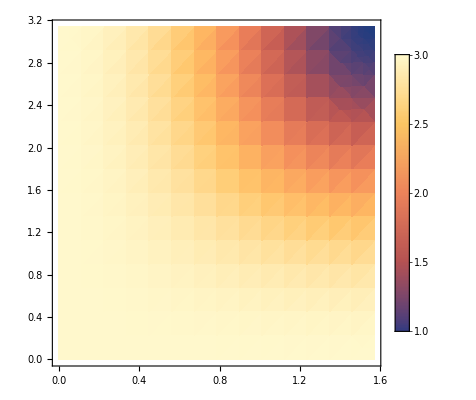

```mathematica
DensityPlot[1/32 (85+12 Cos[2 x1]-Cos[4 x1]-8 (-3+Cos[2 x1]) Cos[z1] Sin[x1]^2-8 Cos[z1]^2 Sin[x1]^4),{x1,0,Pi/2},{z1,0,Pi},PlotLegends->Automatic]
```

```mathematica
(ascore[a,b,0,x1,y1,z1,x2,y2,z2]//Simplify//FullSimplify)/.{x2->x1,y2->y1,z2->z1}//FullSimplify
```

1/32 (85+12 Cos[2 x1]-Cos[4 x1]-8 (-3+Cos[2 x1]) Cos[z1] Sin[x1]^2-8 Cos[z1]^2 Sin[x1]^4)

```mathematica
ascore[a,b,0,x1,y1,z1,x2,y2,z2]//Simplify//FullSimplify
```

1/16 (43-7 Cos[2 x1]-1/2 Cos[2 x1-2 x2]+13 Cos[2 x2]-1/2 Cos[2 (x1+x2)]-2 (7+Cos[2 x2]) Cos[z1] Sin[x1]^2-2 Cos[z2] (-13+Cos[2 x1]+2 Cos[z1] Sin[x1]^2) Sin[x2]^2)

```mathematica
Manipulate[
{ascore[a,b,γ,x1,y1,z1,x2,y2,z2],bscore[a,b,γ,x1,y1,z1,x2,y2,z2]},Evaluate[Sequence@@varspecs]]
```

```mathematica
varspecs = {
{a,0,10},
{γ,0,Pi/2}};

Manipulate[
DensityPlot3D[ascore[a,a,γ,x1,y1,z1,x1,y1,z1],{x1,0,2Pi},{y1,0,2Pi},{z1,0,2Pi},PlotRange->{0,5}],Evaluate[Sequence@@varspecs]]
```

```mathematica
varspecs = {
{aa,0,10},
{bb,0,10},
{γγ,0,Pi/2},
{xx1,0,Pi},
{yy1,0,Pi},
{zz1,0,Pi},
{xx2,0,Pi},
{yy2,0,Pi},
{zz2,0,Pi}};
repRules = {a->aa,b->bb,γ->γγ,x1->xx1,y1->yy1,z1->z1,x2->xx2,y2->yy2,z2->zz2};
With[{a=2},a]
```

2

```mathematica
snack=chips
```

chips

```mathematica
With[{chips=2},snack//Evaluate]
```

2

```mathematica
Manipulate[ascore/.repRules,Evaluate[Sequence@@varspecs]]
```

```mathematica
Manipulate[,
{a,0,10},
{b,0,10},
{γ,0,Pi/2},
{x1,0,Pi},
{y1,0,Pi},
{z1,0,Pi},
{x2,0,Pi},
{y2,0,Pi},
{z2,0,Pi}
]
```

```mathematica
fullPlay[[1]]//FullSimplify
```

```mathematica
ArgAbs[n_]:={Arg[n],Abs[n]}
```

```mathematica
alicesScore[fullPlay]/.Conjugate->myFunc//Simplify
```

-1/4096 ⅇ^(-2 ⅈ (2 x1+2 y1+z1+γ)) (-1+ⅇ^(ⅈ z1))^2 (1-2 ⅇ^(2 ⅈ x1)+ⅇ^(4 ⅈ x1)+8 ⅇ^(3 ⅈ x1+2 ⅈ y1)-ⅇ^(4 ⅈ y1)-ⅇ^(4 ⅈ (x1+y1))+8 ⅇ^(ⅈ (x1+2 y1))+2 ⅇ^(2 ⅈ (x1+2 y1))-ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (2 x1+z1))-ⅇ^(ⅈ (4 x1+z1))+8 ⅇ^(ⅈ (x1+2 y1+z1))+8 ⅇ^(ⅈ (3 x1+2 y1+z1))+ⅇ^(ⅈ (4 y1+z1))-2 ⅇ^(ⅈ (2 x1+4 y1+z1))+ⅇ^(ⅈ (4 x1+4 y1+z1))+2 ⅇ^(ⅈ γ)+ⅇ^(2 ⅈ γ)-2 ⅇ^(2 ⅈ (x1+γ))-4 ⅇ^(ⅈ (2 x1+γ))+ⅇ^(2 ⅈ (2 x1+γ))+2 ⅇ^(ⅈ (4 x1+γ))-ⅇ^(2 ⅈ (2 y1+γ))+2 ⅇ^(2 ⅈ (x1+2 y1+γ))-ⅇ^(2 ⅈ (2 x1+2 y1+γ))+2 ⅇ^(ⅈ (4 y1+γ))-4 ⅇ^(ⅈ (2 x1+4 y1+γ))+2 ⅇ^(ⅈ (4 x1+4 y1+γ))-2 ⅇ^(ⅈ (z1+γ))+4 ⅇ^(ⅈ (2 x1+z1+γ))-2 ⅇ^(ⅈ (4 x1+z1+γ))-2 ⅇ^(ⅈ (4 y1+z1+γ))+4 ⅇ^(ⅈ (2 x1+4 y1+z1+γ))-2 ⅇ^(ⅈ (4 x1+4 y1+z1+γ))-ⅇ^(ⅈ (z1+2 γ))+2 ⅇ^(ⅈ (2 x1+z1+2 γ))-ⅇ^(ⅈ (4 x1+z1+2 γ))-8 ⅇ^(ⅈ (x1+2 y1+z1+2 γ))-8 ⅇ^(ⅈ (3 x1+2 y1+z1+2 γ))+ⅇ^(ⅈ (4 y1+z1+2 γ))-2 ⅇ^(ⅈ (2 x1+4 y1+z1+2 γ))+ⅇ^(ⅈ (4 x1+4 y1+z1+2 γ))-8 ⅇ^(ⅈ (x1+2 (y1+γ)))-8 ⅇ^(ⅈ (3 x1+2 (y1+γ)))) (1-2 ⅇ^(2 ⅈ x1)+ⅇ^(4 ⅈ x1)-8 ⅇ^(3 ⅈ x1+2 ⅈ y1)-ⅇ^(4 ⅈ y1)-ⅇ^(4 ⅈ (x1+y1))-8 ⅇ^(ⅈ (x1+2 y1))+2 ⅇ^(2 ⅈ (x1+2 y1))-ⅇ^(ⅈ z1)+2 ⅇ^(ⅈ (2 x1+z1))-ⅇ^(ⅈ (4 x1+z1))-8 ⅇ^(ⅈ (x1+2 y1+z1))-8 ⅇ^(ⅈ (3 x1+2 y1+z1))+ⅇ^(ⅈ (4 y1+z1))-2 ⅇ^(ⅈ (2 x1+4 y1+z1))+ⅇ^(ⅈ (4 x1+4 y1+z1))-2 ⅇ^(ⅈ γ)+ⅇ^(2 ⅈ γ)-2 ⅇ^(2 ⅈ (x1+γ))+4 ⅇ^(ⅈ (2 x1+γ))+ⅇ^(2 ⅈ (2 x1+γ))-2 ⅇ^(ⅈ (4 x1+γ))-ⅇ^(2 ⅈ (2 y1+γ))+2 ⅇ^(2 ⅈ (x1+2 y1+γ))-ⅇ^(2 ⅈ (2 x1+2 y1+γ))-2 ⅇ^(ⅈ (4 y1+γ))+4 ⅇ^(ⅈ (2 x1+4 y1+γ))-2 ⅇ^(ⅈ (4 x1+4 y1+γ))+2 ⅇ^(ⅈ (z1+γ))-4 ⅇ^(ⅈ (2 x1+z1+γ))+2 ⅇ^(ⅈ (4 x1+z1+γ))+2 ⅇ^(ⅈ (4 y1+z1+γ))-4 ⅇ^(ⅈ (2 x1+4 y1+z1+γ))+2 ⅇ^(ⅈ (4 x1+4 y1+z1+γ))-ⅇ^(ⅈ (z1+2 γ))+2 ⅇ^(ⅈ (2 x1+z1+2 γ))-ⅇ^(ⅈ (4 x1+z1+2 γ))+8 ⅇ^(ⅈ (x1+2 y1+z1+2 γ))+8 ⅇ^(ⅈ (3 x1+2 y1+z1+2 γ))+ⅇ^(ⅈ (4 y1+z1+2 γ))-2 ⅇ^(ⅈ (2 x1+4 y1+z1+2 γ))+ⅇ^(ⅈ (4 x1+4 y1+z1+2 γ))+8 ⅇ^(ⅈ (x1+2 (y1+γ)))+8 ⅇ^(ⅈ (3 x1+2 (y1+γ))))+1/4096 3 ⅇ^(-2 ⅈ (2 x1+2 y1+z1+γ)) (1-2 ⅇ^(2 ⅈ x1)+ⅇ^(4 ⅈ x1)+8 ⅇ^(3 ⅈ x1+2 ⅈ y1)-ⅇ^(4 ⅈ y1)-ⅇ^(4 ⅈ (x1+y1))+8 ⅇ^(ⅈ (x1+2 y1))+2 ⅇ^(2 ⅈ (x1+2 y1))-2 ⅇ^(ⅈ z1)+ⅇ^(2 ⅈ z1)-2 ⅇ^(2 ⅈ (x1+z1))+4 ⅇ^(ⅈ (2 x1+z1))+ⅇ^(2 ⅈ (2 x1+z1))-2 ⅇ^(ⅈ (4 x1+z1))-ⅇ^(2 ⅈ (2 y1+z1))+2 ⅇ^(2 ⅈ (x1+2 y1+z1))-ⅇ^(2 ⅈ (2 x1+2 y1+z1))+2 ⅇ^(ⅈ (4 y1+z1))-4 ⅇ^(ⅈ (2 x1+4 y1+z1))+2 ⅇ^(ⅈ (4 x1+4 y1+z1))-8 ⅇ^(ⅈ (x1+2 (y1+z1)))-8 ⅇ^(ⅈ (3 x1+2 (y1+z1)))-ⅇ^(2 ⅈ γ)+2 ⅇ^(2 ⅈ (x1+γ))-ⅇ^(2 ⅈ (2 x1+γ))-4 ⅇ^(ⅈ (2 y1+γ))+ⅇ^(2 ⅈ (2 y1+γ))-2 ⅇ^(2 ⅈ (x1+2 y1+γ))-24 ⅇ^(ⅈ (2 x1+2 y1+γ))+ⅇ^(2 ⅈ (2 x1+2 y1+γ))-4 ⅇ^(ⅈ (4 x1+2 y1+γ))-ⅇ^(2 ⅈ (z1+γ))+2 ⅇ^(2 ⅈ (x1+z1+γ))-ⅇ^(2 ⅈ (2 x1+z1+γ))+8 ⅇ^(ⅈ (2 y1+z1+γ))+ⅇ^(2 ⅈ (2 y1+z1+γ))-2 ⅇ^(2 ⅈ (x1+2 y1+z1+γ))-16 ⅇ^(ⅈ (2 x1+2 y1+z1+γ))+ⅇ^(2 ⅈ (2 x1+2 y1+z1+γ))+8 ⅇ^(ⅈ (4 x1+2 y1+z1+γ))-4 ⅇ^(ⅈ (2 y1+2 z1+γ))-24 ⅇ^(ⅈ (2 x1+2 y1+2 z1+γ))-4 ⅇ^(ⅈ (4 x1+2 y1+2 z1+γ))+2 ⅇ^(ⅈ (z1+2 γ))-4 ⅇ^(ⅈ (2 x1+z1+2 γ))+2 ⅇ^(ⅈ (4 x1+z1+2 γ))-2 ⅇ^(ⅈ (4 y1+z1+2 γ))+4 ⅇ^(ⅈ (2 x1+4 y1+z1+2 γ))-2 ⅇ^(ⅈ (4 x1+4 y1+z1+2 γ))+8 ⅇ^(ⅈ (x1+2 (y1+γ)))+8 ⅇ^(ⅈ (3 x1+2 (y1+γ)))-8 ⅇ^(ⅈ (x1+2 (y1+z1+γ)))-8 ⅇ^(ⅈ (3 x1+2 (y1+z1+γ)))) (1-2 ⅇ^(2 ⅈ x1)+ⅇ^(4 ⅈ x1)-8 ⅇ^(3 ⅈ x1+2 ⅈ y1)-ⅇ^(4 ⅈ y1)-ⅇ^(4 ⅈ (x1+y1))-8 ⅇ^(ⅈ (x1+2 y1))+2 ⅇ^(2 ⅈ (x1+2 y1))-2 ⅇ^(ⅈ z1)+ⅇ^(2 ⅈ z1)-2 ⅇ^(2 ⅈ (x1+z1))+4 ⅇ^(ⅈ (2 x1+z1))+ⅇ^(2 ⅈ (2 x1+z1))-2 ⅇ^(ⅈ (4 x1+z1))-ⅇ^(2 ⅈ (2 y1+z1))+2 ⅇ^(2 ⅈ (x1+2 y1+z1))-ⅇ^(2 ⅈ (2 x1+2 y1+z1))+2 ⅇ^(ⅈ (4 y1+z1))-4 ⅇ^(ⅈ (2 x1+4 y1+z1))+2 ⅇ^(ⅈ (4 x1+4 y1+z1))+8 ⅇ^(ⅈ (x1+2 (y1+z1)))+8 ⅇ^(ⅈ (3 x1+2 (y1+z1)))-ⅇ^(2 ⅈ γ)+2 ⅇ^(2 ⅈ (x1+γ))-ⅇ^(2 ⅈ (2 x1+γ))-4 ⅇ^(ⅈ (2 y1+γ))+ⅇ^(2 ⅈ (2 y1+γ))-2 ⅇ^(2 ⅈ (x1+2 y1+γ))-24 ⅇ^(ⅈ (2 x1+2 y1+γ))+ⅇ^(2 ⅈ (2 x1+2 y1+γ))-4 ⅇ^(ⅈ (4 x1+2 y1+γ))-ⅇ^(2 ⅈ (z1+γ))+2 ⅇ^(2 ⅈ (x1+z1+γ))-ⅇ^(2 ⅈ (2 x1+z1+γ))+8 ⅇ^(ⅈ (2 y1+z1+γ))+ⅇ^(2 ⅈ (2 y1+z1+γ))-2 ⅇ^(2 ⅈ (x1+2 y1+z1+γ))-16 ⅇ^(ⅈ (2 x1+2 y1+z1+γ))+ⅇ^(2 ⅈ (2 x1+2 y1+z1+γ))+8 ⅇ^(ⅈ (4 x1+2 y1+z1+γ))-4 ⅇ^(ⅈ (2 y1+2 z1+γ))-24 ⅇ^(ⅈ (2 x1+2 y1+2 z1+γ))-4 ⅇ^(ⅈ (4 x1+2 y1+2 z1+γ))+2 ⅇ^(ⅈ (z1+2 γ))-4 ⅇ^(ⅈ (2 x1+z1+2 γ))+2 ⅇ^(ⅈ (4 x1+z1+2 γ))-2 ⅇ^(ⅈ (4 y1+z1+2 γ))+4 ⅇ^(ⅈ (2 x1+4 y1+z1+2 γ))-2 ⅇ^(ⅈ (4 x1+4 y1+z1+2 γ))-8 ⅇ^(ⅈ (x1+2 (y1+γ)))-8 ⅇ^(ⅈ (3 x1+2 (y1+γ)))+8 ⅇ^(ⅈ (x1+2 (y1+z1+γ)))+8 ⅇ^(ⅈ (3 x1+2 (y1+z1+γ))))+1/1024 5 (-1+ⅇ^(-2 ⅈ x1)) (-1+ⅇ^(2 ⅈ x1)) (-1+ⅇ^(-ⅈ z1)) (-1+ⅇ^(ⅈ z1)) (1-2 ⅇ^(ⅈ x1)+ⅇ^(2 ⅈ x1)-ⅇ^(2 ⅈ y1)-ⅇ^(2 ⅈ (x1+y1))-2 ⅇ^(ⅈ (x1+2 y1))-ⅇ^(ⅈ z1)-2 ⅇ^(ⅈ (x1+z1))-ⅇ^(ⅈ (2 x1+z1))+ⅇ^(ⅈ (2 y1+z1))-2 ⅇ^(ⅈ (x1+2 y1+z1))+ⅇ^(ⅈ (2 x1+2 y1+z1))-ⅇ^(ⅈ γ)+2 ⅇ^(ⅈ (x1+γ))-ⅇ^(ⅈ (2 x1+γ))-ⅇ^(ⅈ (2 y1+γ))-2 ⅇ^(ⅈ (x1+2 y1+γ))-ⅇ^(ⅈ (2 x1+2 y1+γ))+ⅇ^(ⅈ (z1+γ))+2 ⅇ^(ⅈ (x1+z1+γ))+ⅇ^(ⅈ (2 x1+z1+γ))+ⅇ^(ⅈ (2 y1+z1+γ))-2 ⅇ^(ⅈ (x1+2 y1+z1+γ))+ⅇ^(ⅈ (2 x1+2 y1+z1+γ))) (1-2 ⅇ^(-ⅈ x1)+ⅇ^(-2 ⅈ x1)-ⅇ^(-2 ⅈ y1)-ⅇ^(-2 ⅈ (x1+y1))-ⅇ^(-ⅈ z1)-2 ⅇ^(-ⅈ (x1+z1))-ⅇ^(-ⅈ γ)+2 ⅇ^(-ⅈ (x1+γ))+ⅇ^(-ⅈ (z1+γ))+2 ⅇ^(-ⅈ (x1+z1+γ))-2 Cos[x1+2 y1]-Cos[2 x1+z1]+Cos[2 y1+z1]-2 Cos[x1+2 y1+z1]+Cos[2 x1+2 y1+z1]-Cos[2 x1+γ]-Cos[2 y1+γ]-2 Cos[x1+2 y1+γ]-Cos[2 x1+2 y1+γ]+Cos[2 x1+z1+γ]+Cos[2 y1+z1+γ]-2 Cos[x1+2 y1+z1+γ]+Cos[2 x1+2 y1+z1+γ]+ⅈ (2 Sin[x1+2 y1]+Sin[2 x1+z1]-Sin[2 y1+z1]+2 Sin[x1+2 y1+z1]-Sin[2 x1+2 y1+z1]+Sin[2 x1+γ]+Sin[2 y1+γ]+2 Sin[x1+2 y1+γ]+Sin[2 x1+2 y1+γ]-Sin[2 x1+z1+γ]-Sin[2 y1+z1+γ]+2 Sin[x1+2 y1+z1+γ]-Sin[2 x1+2 y1+z1+γ]))

```mathematica
fullPlay[[1]]
```

1/8 ⅇ^(ⅈ z1) (10-2 Cos[2 x1]+Cos[2 x1-z1]+22 Cos[z1]+Cos[2 x1+z1]-4 (1+3 Cos[2 x1]) Cos[2 a γ] Sin[z1/2]^2-32 ⅈ Cos[x1] Cos[γ] Cos[a γ] Sin[z1])-(-1+ⅇ^(ⅈ z1))^2 Cos[a γ] Sin[x1]^2 Sin[2 y1] Sin[γ]-(-1+ⅇ^(ⅈ z1))^2 Sin[2 x1] Sin[y1] Sin[γ] Sin[a γ]+1/2 (-1+ⅇ^(ⅈ z1))^2 Cos[2 y1] Sin[x1]^2 Sin[a γ]^2+2 ⅇ^(ⅈ z1) Cos[y1] (2 ⅈ Cos[γ] Sin[x1] Sin[z1] Sin[a γ]+Sin[2 x1] Sin[z1/2]^2 Sin[2 a γ])

```mathematica
Manipulate
```

```mathematica
aliceMove//MatrixForm
```

(Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2] | Sin[x1] (-ⅈ Cos[y1]-Sin[y1]) Sin[z1/2]
Sin[x1] (-ⅈ Cos[y1]+Sin[y1]) Sin[z1/2] | Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2])

```mathematica
aliceMove = (su2[x1,y1,z1])//FullSimplify;
bobsMove = (su2[x2,y1,z2])//FullSimplify;
```

```mathematica
play[J_,d1_,d2_]:=ConjugateTranspose[J].(KroneckerProduct[d1,d2].(J.{1,0,0,0}))
```